```mathematica
α:=1
r0:=1
γ:=1
Manipulate[LogLogPlot[α (r/r0)^-γ,{r,0.01,200},PlotRange->{{0.1,100},{0.1,100}},Epilog->{PointSize[0.03],Red,Point[{Log[r0],Log[α]}]}],{{α,1},1,10},{{r0,1},0.1,10},{{γ,1},0,10}]
```

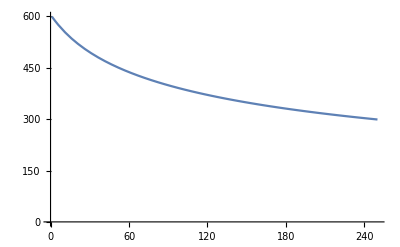

```mathematica
vout[r_,v1_,A_,Rs_]:=√(v1^2+A(-Log[(Rs+1)/Rs]+1/r Log[(Rs+r)/Rs]))
Plot[vout[r,600,10^7,27],{r,1,250},AxesOrigin->{0,0}]
```

```mathematica
Manipulate[Plot[vout[r,v1,A,Rs],{r,1,250},PlotRange->{{0,250},{0,800}}],{{v1,600},100,800},{{A,10^7},10^5,10^8},{{Rs,27},0,50}]
```

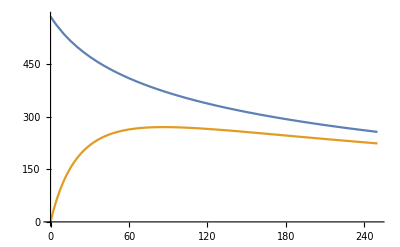

```mathematica
vcircsimp[r_,Rs_]:=-1/(r+Rs)+Log[(r+Rs)/Rs]/r
Plot[{vout[r,580,10^7,27],50000*vcircsimp[r,40]},{r,0,250},AxesOrigin->{0,0}]
```